```mathematica
Map[StandardDeviation,IntegerPartitions[17,{4}]]//N//Sort
```

{0.5,0.957427,1.25831,1.5,1.5,1.70783,1.89297,2.06155,2.06155,2.21736,2.21736,2.36291,2.5,2.5,2.62996,2.62996,2.75379,2.87228,2.87228,2.98608,3.20156,3.20156,3.30404,3.30404,3.40343,3.59398,3.77492,3.86221,3.94757,3.94757,4.03113,4.272,4.5,4.57347,4.71699,5.18813,5.25198,5.85235,6.5}

```mathematica
Select[IntegerPartitions[17,{4}],StandardDeviation[#]<1&]
```

{{5,5,4,3},{5,4,4,4}}

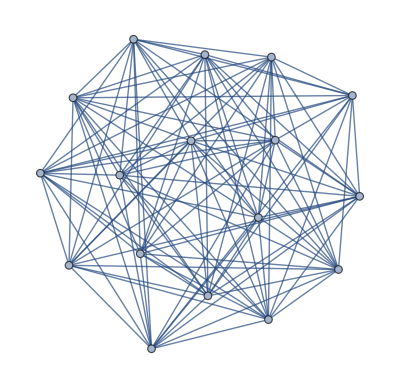

```mathematica
g=Graph[GraphFromSets[{{1,2,3,4,5},{6,7,8,9},{10,11,12,13},{14,15,16,17}}]]
```

```mathematica
Subgraph
```

```mathematica
GraphSignature2[g]
```

13-13-13-13-13-13-13-13-13-13-13-13-12-12-12-12-12

```mathematica
GraphSignature2[Graph[plantri[[8]]]]
```

6-6-6-6-6-5-5-5-5-5-5-5-5-5-5-5-5

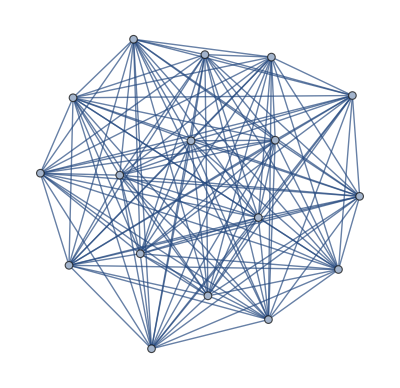

```mathematica
GraphPower[g,3]
```

```mathematica
IsomorphicGraphQ[g,GraphPower[g,3]]
```

False

```mathematica
GraphRadius[g]
```

2

```mathematica
GraphDiameter[g]
```

2

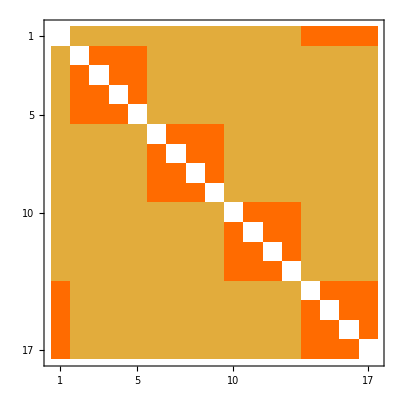

```mathematica
GraphDistanceMatrix[g]//MatrixPlot
```

```mathematica
FindShortestPath[g,All,All]
```

ShortestPathFunction[{All,All},«»]

```mathematica
GraphPeriphery[g]
```

{1,6,7,8,9,10,11,12,13,14,15,16,17,2,3,4,5}

```mathematica
GraphCenter[g]
```

{1,6,7,8,9,10,11,12,13,14,15,16,17,2,3,4,5}

```mathematica
FindVertexCover[g]
```

{6,7,8,9,10,11,12,13,14,15,16,17}

```mathematica
FindIndependentEdgeSet[g]
```

{1<->6,7<->4,8<->3,9<->17,10<->2,11<->16,12<->15,13<->14}

```mathematica
FindClique[g]
```

{{1,6,10,14}}

```mathematica
FindHamiltonianCycle[g]
```

{{1<->14,14<->5,5<->7,7<->17,17<->9,9<->13,13<->16,16<->10,10<->2,2<->15,15<->8,8<->11,11<->3,3<->6,6<->4,4<->12,12<->1}}

```mathematica
AcyclicGraphQ[g]
```

False

```mathematica
AdjacencyMatrix[g]//MatrixRank
```

4

```mathematica
DiscreteWaveletTransform[%117]
```

DiscreteWaveletTransform::wlist: Argument Null should be one of rectangular array of any depth, image, sound, or sampled sound list.

DiscreteWaveletTransform[Null]

```mathematica
f=ChromaticPolynomial[g,x]
```

3115886526018 x-10914405301011 x^2+16624444433937 x^3-14841254017668 x^4+8786053151034 x^5-3687190723723 x^6+1141986128374 x^7-267671853758 x^8+48200119355 x^9-6716370756 x^10+724335564 x^11-60017520 x^12+3757071 x^13-172284 x^14+5474 x^15-108 x^16+x^17

```mathematica
f/.x->4
```

24

```mathematica
f/.x->5
```

4440

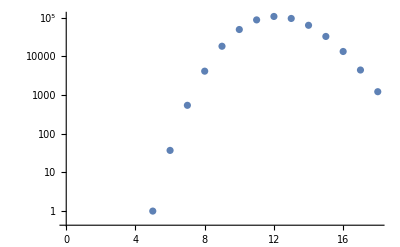

```mathematica
Table[(3115886526018 x-10914405301011 x^2+16624444433937 x^3-14841254017668 x^4+8786053151034 x^5-3687190723723 x^6+1141986128374 x^7-267671853758 x^8+48200119355 x^9-6716370756 x^10+724335564 x^11-60017520 x^12+3757071 x^13-172284 x^14+5474 x^15-108 x^16+x^17)/x!,{x,0,17}]//ListLogPlot
```

```mathematica
CompleteBaseCoeff[3115886526018 x-10914405301011 x^2+16624444433937 x^3-14841254017668 x^4+8786053151034 x^5-3687190723723 x^6+1141986128374 x^7-267671853758 x^8+48200119355 x^9-6716370756 x^10+724335564 x^11-60017520 x^12+3757071 x^13-172284 x^14+5474 x^15-108 x^16+x^17]
```

{0,0,0,0,1,36,505,3608,14338,33040,46501,41587,24150,9145,2226,334,28,1}

```mathematica
NullBaseCoeff[3115886526018 x-10914405301011 x^2+16624444433937 x^3-14841254017668 x^4+8786053151034 x^5-3687190723723 x^6+1141986128374 x^7-267671853758 x^8+48200119355 x^9-6716370756 x^10+724335564 x^11-60017520 x^12+3757071 x^13-172284 x^14+5474 x^15-108 x^16+x^17]
```

{0,3115886526018,-10914405301011,16624444433937,-14841254017668,8786053151034,-3687190723723,1141986128374,-267671853758,48200119355,-6716370756,724335564,-60017520,3757071,-172284,5474,-108,1}

```mathematica
PathBaseCoeff[3115886526018 x-10914405301011 x^2+16624444433937 x^3-14841254017668 x^4+8786053151034 x^5-3687190723723 x^6+1141986128374 x^7-267671853758 x^8+48200119355 x^9-6716370756 x^10+724335564 x^11-60017520 x^12+3757071 x^13-172284 x^14+5474 x^15-108 x^16+x^17]
```

{0,0,-171026005534,591120193551,-884912821204,773168803892,-445869936169,181285524854,-54047695938,12098769080,-2060176308,267999464,-26521336,1968193,-106428,3974,-92,1}

```mathematica
JacobsthalBaseCoeff[3115886526018 x-10914405301011 x^2+16624444433937 x^3-14841254017668 x^4+8786053151034 x^5-3687190723723 x^6+1141986128374 x^7-267671853758 x^8+48200119355 x^9-6716370756 x^10+724335564 x^11-60017520 x^12+3757071 x^13-172284 x^14+5474 x^15-108 x^16+x^17]
```

{0,0,0,1495116951,1495116949,-938408101,-513776742,1166543493,-863261962,381471203,-114266372,24379377,-3777669,425264,-34143,1868,-63,1}

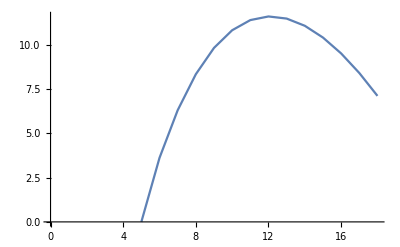

```mathematica
Table[Log[(3115886526018 x-10914405301011 x^2+16624444433937 x^3-14841254017668 x^4+8786053151034 x^5-3687190723723 x^6+1141986128374 x^7-267671853758 x^8+48200119355 x^9-6716370756 x^10+724335564 x^11-60017520 x^12+3757071 x^13-172284 x^14+5474 x^15-108 x^16+x^17)/x!],{x,0,17}]//ListLinePlot
```